# Visualizing scalar fields

Katharine Long
Math & Stats, TTU, 2024

## Contour and surface plots in Cartesian coordinates

```mathematica
f[x_,y_]=1/Sqrt[1+ (x-y)^2 + 4(x+y)^2]
```

1/(√((x-y)^2+4 (x+y)^2+1))

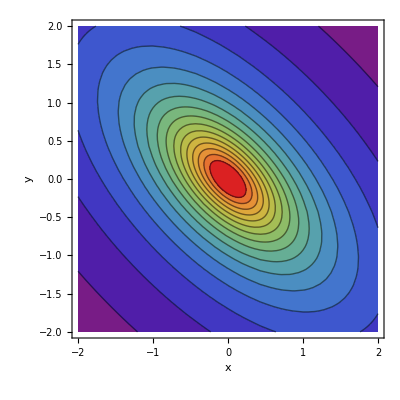

```mathematica
ContourPlot[f[x,y],{x,-2,2},{y,-2,2},Contours->16,FrameLabel->{"x","y"}]
```

```mathematica
Plot3D[f[x,y],{x,-2,2},{y,-2,2},AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
Plot3D[f[x,y],{x,-2,2},{y,-2,2},AxesLabel->{"x","y","z"},PlotTheme->"ZMesh"]
```

-Graphics3D-

```mathematica
g[x_,y_]=Sin[(3/2)Pi x]Sinh[(3/2)Pi y]/Sinh[(3/2)Pi]
```

csch((3 π)/2) sin((3 π x)/2) sinh((3 π y)/2)

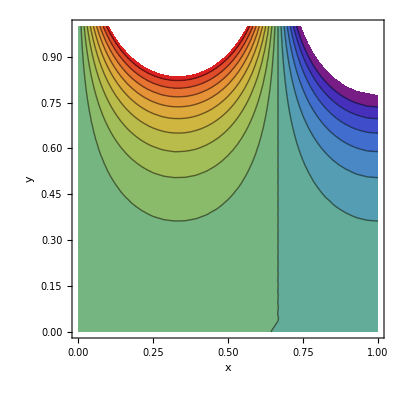

```mathematica
ContourPlot[g[x,y],{x,0,1},{y,0,1},Contours->16,FrameLabel->{"x","y"}]
```

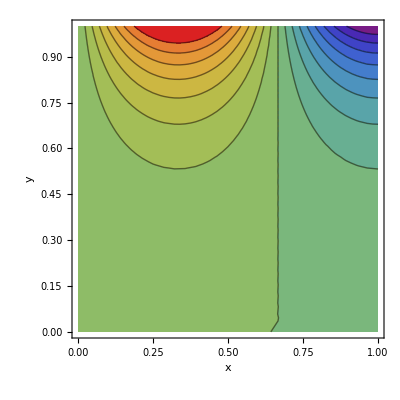

```mathematica
ContourPlot[g[x,y],{x,0,1},{y,0,1},Contours->16,FrameLabel->{"x","y"},PlotRange->All]
```

```mathematica
Plot3D[g[x,y],{x,0,1},{y,0,1},AxesLabel->{"x","y","z"},PlotTheme->"ZMesh"]
```

-Graphics3D-

```mathematica
Plot3D[g[x,y],{x,0,1},{y,0,1},AxesLabel->{"x","y","z"},PlotTheme->"ZMesh",PlotRange->All]
```

-Graphics3D-

## Visualization in 3D

```mathematica
f[x_,y_,z_]= x^2 + 2y^2 - z^2
```

x^2+2 y^2-z^2

```mathematica
ContourPlot3D[f[x,y,z],{x,-2,2},{y,-2,2},{z,-2,2},Contours->Table[c,{c,-4,4,2}],AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
DensityPlot3D[f[x,y,z],{x,-2,2},{y,-2,2},{z,-2,2},AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
g[x_,y_,z_]=1/Sqrt[1+ x^2+4(y^2+z^2)]
```

1/(√(x^2+4 (y^2+z^2)+1))

```mathematica
ContourPlot3D[g[x,y,z],{x,0,2},{y,0,2},{z,0,2},Contours->Table[c,{c,0.1,0.9,0.1}],AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
DensityPlot3D[g[x,y,z],{x,0,2},{y,0,2},{z,0,2},AxesLabel->{"x","y","z"}]
```

-Graphics3D-

## Contour and surface plots in 2D polar coordinates

```mathematica
rho[x_,y_]=Sqrt[x^2+y^2]
```

√(x^2+y^2)

```mathematica
phi[x_,y_]=ArcTan[x,y]
```

tan^-1(x,y)

### Plotting on a disk

```mathematica
u[ρ_,ϕ_]=Sqrt[1 + ρ^2 (1+1/2 Cos[ϕ]^3)] (1+2Cos[2ϕ-Pi/3]/Sqrt[1+ρ^2/16])
```

((2 sin(2 ϕ+π/6))/(√(ρ^2/16+1))+1) √(ρ^2 ((cos^3(ϕ))/2+1)+1)

```mathematica
disk = Disk[{0,0},10]
```

Disk[{0,0},10]

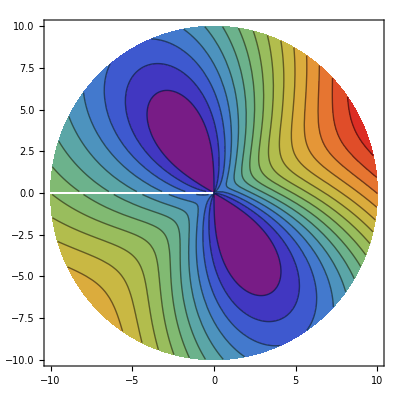

```mathematica
ContourPlot[
u[rho[x,y],phi[x,y]],
{x,y}∈ disk,Contours->16]
```

```mathematica
Plot3D[
u[rho[x,y],phi[x,y]],
{x,y}∈ disk,PlotTheme->"ZMesh"]
```

-Graphics3D-

### Plotting on an annulus between concentric circles

```mathematica
v[ρ_,ϕ_]= ρ^2 Cos[2ϕ] -  Cos[3 (ϕ - Pi/4)]/4/ρ^3
```

ρ^2 cos(2 ϕ)-(cos(3 (ϕ-π/4)))/(4 ρ^3)

```mathematica
reg = Annulus[{0,0},{1/2,2}]
```

Annulus[{0,0},{1/2,2}]

```mathematica
rho[x_,y_]=Sqrt[x^2+y^2]
```

√(x^2+y^2)

```mathematica
phi[x_,y_]=ArcTan[x,y]
```

tan^-1(x,y)

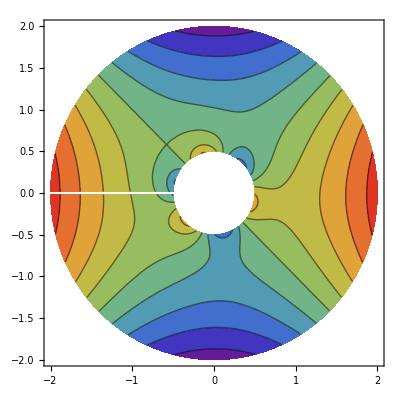

```mathematica
ContourPlot[
v[rho[x,y],phi[x,y]],
{x,y}∈ reg,Contours->16]
```

```mathematica
Plot3D[v[rho[x,y],phi[x,y]],{x,y}∈ reg,PlotTheme->"ZMesh"]
```

-Graphics3D-